### Define functions to create experimental designs (prey and predator abundance levels)

Linear series of prey abundance levels (starting at 3 for prey and 1 for predators)

```mathematica
PreyVals[n_]:=Table[i,{i,3,n+2}]
PredVals[n_]:=Table[i,{i,1,n}]

PreyVals[10]
PredVals[10]
```

{3,4,5,6,7,8,9,10,11,12}

{1,2,3,4,5,6,7,8,9,10}

Fibonacci series of prey abundance levels (starting at 3 for prey and 1 for predators)
(Note that Fibonacci[i] gives the ith Fibonacci number.)

```mathematica
PreyVals[n_]:=Table[Fibonacci[i],{i,4,n+3}] 
PredVals[n_]:=Table[Fibonacci[i],{i,2,n+1}]

PreyVals[10]
PredVals[10]
```

{3,5,8,13,21,34,55,89,144,233}

{1,2,3,5,8,13,21,34,55,89}

Functions to create equidistant points in log-space

```mathematica
logSpace[a_?Positive,b_?Positive,n_]:=Exp@Range[Log@a,Log@b,Log[b/a]/(n-1)]
log2Space[a_,b_,n_]:=2^Range[a,b,(b-a)/(n-1)]
logGRSpace[a_,b_,n_]:=Round[GoldenRatio^Range[a,b,(b-a)/(n-1)]]
```

```mathematica
log2Space[1,10,10]
logGRSpace[0,10,10]
```

{2,4,8,16,32,64,128,256,512,1024}

{1,2,3,5,8,14,25,42,72,123}

GoldenRatio series of prey abundance levels (starting at 3 for prey and 1 for predators)
enabling the generation of arbitrary numbers of equidistant points between min and (specified) max abundances.
The series will be approximately Fibonacci when PreyMax is set to Fibonacci[n] for a desired series length n.

```mathematica
PreyVals[n_,PreyMax_]:=logGRSpace[2,Log[GoldenRatio,PreyMax]+3,n];
PredVals[n_,PredMax_]:=logGRSpace[0,Log[GoldenRatio,PredMax]+1,n];

PreyVals[10,Fibonacci[10]]

PredVals[10,Fibonacci[10]]

PredVals[8,Fibonacci[10]]
PredVals[6,Fibonacci[10]]
PredVals[3,Fibonacci[10]]
```

{3,4,7,12,19,32,52,86,141,233}

{1,2,3,4,7,12,20,33,54,89}

{1,2,4,7,13,25,47,89}

{1,2,6,15,36,89}

{1,9,89}

Example use for generating series of increasing length and increasing maximum value:

```mathematica
Table[
{PreyVals[i,Fibonacci[i]],PredVals[j,Fibonacci[j]]},
{i, 5,12},{j,2,2}
];
%//TableForm
```

3 | 4 | 7 | 13 | 21
1 | 2 |  |  | 
3 | 4 | 7 | 12 | 20 | 34
1 | 2 |  |  |  | 
3 | 4 | 7 | 12 | 20 | 33 | 55
1 | 2 |  |  |  |  | 
3 | 4 | 7 | 12 | 20 | 32 | 54 | 89
1 | 2 |  |  |  |  |  | 
3 | 4 | 7 | 12 | 19 | 32 | 53 | 87 | 144
1 | 2 |  |  |  |  |  |  | 
3 | 4 | 7 | 12 | 19 | 32 | 52 | 86 | 141 | 233
1 | 2 |  |  |  |  |  |  |  | 
3 | 4 | 7 | 12 | 19 | 31 | 52 | 85 | 140 | 229 | 377
1 | 2 |  |  |  |  |  |  |  |  | 
3 | 4 | 7 | 12 | 19 | 31 | 51 | 84 | 138 | 226 | 372 | 610
1 | 2 |  |  |  |  |  |  |  |  |  |

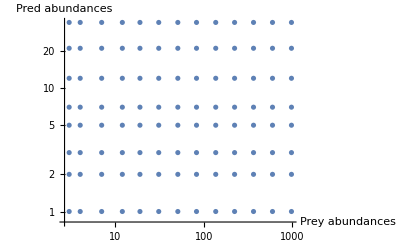

```mathematica
ListPlot[Tuples[{PreyVals[13,Fibonacci[13]],PredVals[8,Fibonacci[8]]}],
ScalingFunctions->{"Log","Log"},
AxesLabel->{"Prey abundances","Pred abundances"}]
```

Example use for generating series of varying length and constant maximum value:

```mathematica
Table[
{PreyVals[i,Fibonacci[13]],PredVals[j,Fibonacci[5]]},
{i, 5,13},{j,2,3}
];
%//TableForm
```

3 | 12 | 51 | 224 | 987
1 | 8 |  |  |  | 3 | 12 | 51 | 224 | 987
1 | 3 | 8 |  | 
3 | 9 | 28 | 92 | 301 | 987
1 | 8 |  |  |  |  | 3 | 9 | 28 | 92 | 301 | 987
1 | 3 | 8 |  |  | 
3 | 7 | 19 | 51 | 137 | 367 | 987
1 | 8 |  |  |  |  |  | 3 | 7 | 19 | 51 | 137 | 367 | 987
1 | 3 | 8 |  |  |  | 
3 | 6 | 14 | 33 | 78 | 181 | 423 | 987
1 | 8 |  |  |  |  |  |  | 3 | 6 | 14 | 33 | 78 | 181 | 423 | 987
1 | 3 | 8 |  |  |  |  | 
3 | 5 | 12 | 24 | 51 | 107 | 224 | 470 | 987
1 | 8 |  |  |  |  |  |  |  | 3 | 5 | 12 | 24 | 51 | 107 | 224 | 470 | 987
1 | 3 | 8 |  |  |  |  |  | 
3 | 5 | 10 | 19 | 37 | 71 | 137 | 264 | 511 | 987
1 | 8 |  |  |  |  |  |  |  |  | 3 | 5 | 10 | 19 | 37 | 71 | 137 | 264 | 511 | 987
1 | 3 | 8 |  |  |  |  |  |  | 
3 | 5 | 9 | 16 | 28 | 51 | 92 | 167 | 301 | 545 | 987
1 | 8 |  |  |  |  |  |  |  |  |  | 3 | 5 | 9 | 16 | 28 | 51 | 92 | 167 | 301 | 545 | 987
1 | 3 | 8 |  |  |  |  |  |  |  | 
3 | 4 | 8 | 13 | 23 | 39 | 67 | 114 | 196 | 336 | 576 | 987
1 | 8 |  |  |  |  |  |  |  |  |  |  | 3 | 4 | 8 | 13 | 23 | 39 | 67 | 114 | 196 | 336 | 576 | 987
1 | 3 | 8 |  |  |  |  |  |  |  |  | 
3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 8 |  |  |  |  |  |  |  |  |  |  |  | 3 | 4 | 7 | 12 | 19 | 31 | 51 | 83 | 137 | 224 | 367 | 602 | 987
1 | 3 | 8 |  |  |  |  |  |  |  |  |  |